```mathematica
(* y''- 2 y'+ y = 0 *)
```

```mathematica
solveEqCaract=Solve[λ^2-2λ+1==0,λ]
```

{{λ→1},{λ→1}}

```mathematica
solveEqCaract[[1,1,2]]
```

1

```mathematica
solveEqCaract[[2,1,2]]
```

1

```mathematica
solHomogenea[x_]=c1 E^(solveEqCaract[[1,1,2]] x)+c2 x E^(solveEqCaract[[2,1,2]]x)
```

c1 ⅇ^x+c2 ⅇ^x x

```mathematica
solHomogenea[0]==3
```

c1==3

```mathematica
D[solHomogenea[x],x]/.c1->3/.x->0
```

3+c2

```mathematica
Solve[3+c2==1,c2]
```

{{c2→-2}}

```mathematica
solHomogFinal[x_]=3 ⅇ^x-2x ⅇ^x
```

3 ⅇ^x-2 ⅇ^x x

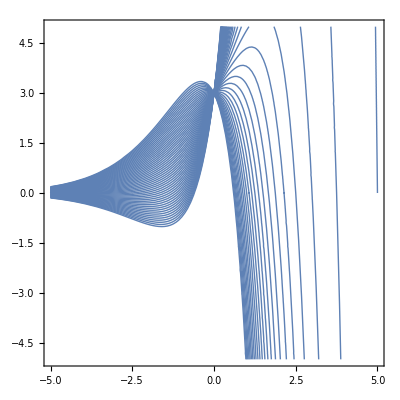

```mathematica
Show[Table[ContourPlot[y==3 ⅇ^x+c2 x ⅇ^x,{x,-5,5},{y,-5,5},ContourStyle->{Thin},AspectRatio->Automatic],{c2,-5,5,.2}]]
```

```mathematica
Show[Table[ContourPlot3D[z==-y+3 ⅇ^x+c2 x ⅇ^x,{x,-3,3},{y,-5,5},{z,-20,20}],{c2,-3,3}]]
```

-Graphics3D-

```mathematica
D[solHomogenea[x],x]
```

c1 ⅇ^x+c2 ⅇ^x+c2 ⅇ^x x

```mathematica
D[solHomogenea[x],x]/.x->0
```

c1+c2

```mathematica
solHomogenea[0]==3
```

c1==3

```mathematica
DSolve[x^2 y''[x]-4x y'[x]+6y[x]==0,y[x],x]
```